FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{{36.2742,0.},{167.296,60.2169},{332.316,54.8682},{442.604,51.5005},{507.989,48.5925},{540.619,45.6393},{546.936,42.2988},{528.835,38.1631},{484.827,32.5558},{411.813,24.1313},{312.535,9.94569},{208.572,0.},{94.7729,0.},{36.7896,0.}}

{{Indeterminate,Indeterminate},{700,55},{1390,55},{2400,55},{3100,55},{3000,55},{3540,48},{Indeterminate,Indeterminate},{1900,0},{Indeterminate,0},{Indeterminate,Indeterminate},{Indeterminate,0},{Indeterminate,0},{Indeterminate,0}}

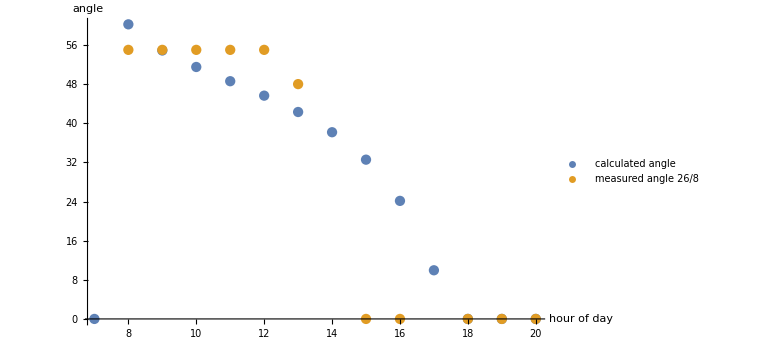

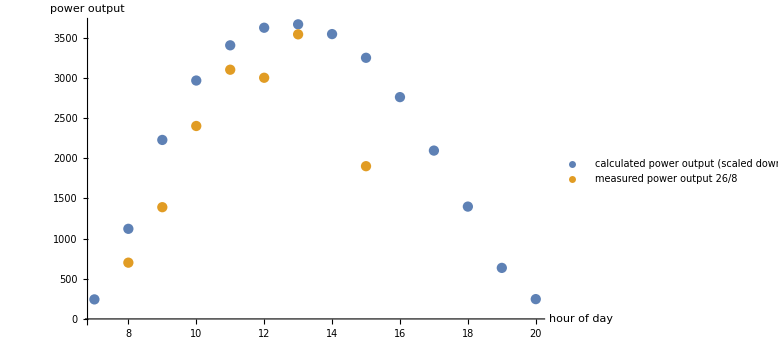

```mathematica
<< SolArduino`

(* Plot measured data (angle, power output) each hour to expected data *)
t = dayAnglesHour[DateObject[{2016,8,26}]]
measuredData = {{Indeterminate,Indeterminate},{700,55},{1390,55},{2400,55},{3100,55},{3000,55},{3540,48},{Indeterminate,Indeterminate},{1900,0},{Indeterminate,0},{Indeterminate,Indeterminate},{Indeterminate,0},{Indeterminate,0},{Indeterminate,0}}
hours = Table[
x,
{x,7,20}
];
ListPlot[{
 Transpose[{hours,t[[All,2]]}],
 Transpose[{hours,measuredData[[All,2]]}]
},
PlotLegends -> {"calculated angle","measured angle 26/8"},
AxesLabel -> {"hour of day","angle"}
,ImageSize -> Large]
ListPlot[{
Transpose[{hours,t[[All,1]]*6.7}],
Transpose[{hours,measuredData[[All,1]]}]
},PlotLegends -> {"calculated power output (scaled down)","measured power output 26/8"},
AxesLabel -> {"hour of day","power output"},ImageSize -> Large
]
```